This Notebook is a test for my master thesis to calculate some Quantum stuff -> for the Redfield equation.

```mathematica
(*Clear previous definitions of operators and symbols*){{ClearAll[bK,bKDagger,omegaK,gK]

(*Define symbolic creation and annihilation operators for each mode k*)
N_modes=5;(*Number of modes*)bK[mode_]:=Symbol["b"<>ToString[mode]];
bKDagger[mode_]:=Symbol["b"<>ToString[mode]<>"†"];

(*Define symbolic frequencies omega_k and coupling constants g_k*)
omegaK[k_]:=Symbol["omega"<>ToString[k]];(*Frequency for mode k*)gK[k_]:=Symbol["g"<>ToString[k]];(*Coupling constant for mode k*)(*Define the Hamiltonian of the bath:H_bath=Sum[omega_k b_k† b_k]*)H_bath=Sum[omegaK[k] bKDagger[k] bK[k],{k,1,N_modes}];

(*Define the coupling operator B=Sum[g_k (b_k†+b_k)]*)
B=Sum[gK[k] (bKDagger[k]+bK[k]),{k,1,N_modes}];

(*Now we define the total Hamiltonian:H_total=H_bath+B*)
(*Use Hold to prevent evaluation until explicitly needed*)
H_total=Hold[H_bath+B];

(*Now check the Hamiltonians to make sure they are correct*)
H_bath
B
H_total

(*Time evolution of the coupling operator B(t) in the Heisenberg picture*)
t=Symbol["t"];(*Time variable*)(*Using Hold to prevent immediate evaluation of the time evolution expression*)B_t=Exp[I H_total t].B.Exp[-I H_total t];

(*Define the density matrix of the bath (thermal state)*)
beta=Symbol["beta"];(*Inverse temperature*)(*Partition function calculation (symbolically)*)Z=Tr[Exp[-beta H_bath],{bK[1],bKDagger[1]}];

(*Define the density matrix for the bath*)
rho_bath=Exp[-beta H_bath]/Z;

(*Compute the correlation function<B(t) B>_Bath*)
correlation=Tr[rho_bath.B_t.B];

(*Simplify the correlation function if needed*)
simplifiedCorrelation=FullSimplify[correlation];

(*Optionally,display the result for the simplified correlation function*)
simplifiedCorrelation}, {□}}
```

Rule::rhs: Pattern H_bath appears on the right-hand side of rule H_total→Hold[H_bath+B].

{{(bk+bk†) gk Null^11 H_bath H_total N_modes Tr[rho_bath.B_t.((bk+bk†) gk N_modes)]},{□}}

```mathematica
(*Define the Bose-Einstein distribution*)BoseEinstein[omega_,T_]:=1/(Exp[omega/T]-1);
```

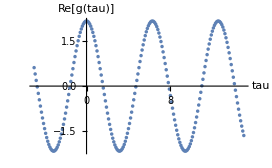

```mathematica
(*Define the correlation function*)
MyCorrelationFunction[tau_,gList_,omegaList_,T_]:=Sum[Abs[gList[[k]]]^2*(BoseEinstein[omegaList[[k]],T]*Exp[-I*omegaList[[k]]*tau]+(BoseEinstein[omegaList[[k]],T]+1)*Exp[I*omegaList[[k]]*tau]),{k,Length[omegaList]}];

(*Example usage*)
gValues={1,0.01,0.2};(*Example coupling strengths*)
omegaValues={1};(*Example frequencies*)
temperature=1;(*Example temperature*)(*Calculate the correlation function for a range of tau values*)
tauValues=Range[-5,15,0.1];
correlationValues=Map[MyCorrelationFunction[#,gValues,omegaValues,temperature]&,tauValues];

(*Plot the correlation function*)
ListPlot[Transpose[{tauValues,Re[correlationValues]}],PlotRange->All,AxesLabel->{"tau","Re[g(tau)]"}]
```

```mathematica
MyCorrelationFunction[]
```

MyCorrelationFunction[]

```mathematica
∫Exp(-x.b2)ⅆx
```

-Exp x x.b2